```mathematica
Clear["Global`*"]
```

```mathematica
1-E^((τ-2 τ0)/μ)-(1-ϵ)/(1+μ √(3ϵ))1/(1+√ϵ)(E^(-√(3ϵ)τ)-E^(τ/μ-(1+μ √(3ϵ))τ0/μ))-(1-ϵ)/(1-μ √(3ϵ))1/(1+√ϵ)(E^(τ/μ-(1+μ √(3ϵ))τ0/μ)-E^((τ-2 τ0)/μ)) /.τ->τ0
1-E^((τ-2 τ0)/μ)-(1-ϵ)/(1+μ √(3ϵ))1/(1+√ϵ)(E^(-√(3ϵ)τ)-E^(τ/μ-(1+μ √(3ϵ))τ0/μ))-(1-ϵ)/(1-μ √(3ϵ))1/(1+√ϵ)(E^(τ/μ-(1+μ √(3ϵ))τ0/μ)-E^((τ-2 τ0)/μ)) /.τ->τ0//FullSimplify
```

1-ⅇ^(-τ0/μ)-((-ⅇ^(-τ0/μ)+ⅇ^(τ0/μ-((1+√3 √ϵ μ) τ0)/μ)) (1-ϵ))/((1+√ϵ) (1-√3 √ϵ μ))-((ⅇ^(-√3 √ϵ τ0)-ⅇ^(τ0/μ-((1+√3 √ϵ μ) τ0)/μ)) (1-ϵ))/((1+√ϵ) (1+√3 √ϵ μ))

```mathematica
1-ⅇ^(-τ0/μ)-((ⅇ^(-√3 √ϵ τ0)-ⅇ^(-τ0/μ)) (1-ϵ))/((1+√ϵ) (1-√3 √ϵ μ))/.{ϵ->0.5, μ->-0.5, τ0->1}
```

-5.10018

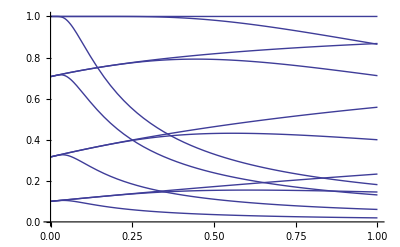

```mathematica
iAnalytic[μ_]:=1-E^(-2 τ0/μ)-(1-ϵ)/(1+μ √(3ϵ))1/(1+√ϵ)(1-E^(-(1+μ √(3ϵ))τ0/μ))-(1-ϵ)/(1-μ √(3ϵ))1/(1+√ϵ)(E^(-(1+μ √(3ϵ))τ0/μ)-E^(-2 τ0/μ))
 
fig3=Plot[ iAnalytic[μ]/.{{ϵ->0.01},{ϵ->0.1},{ ϵ->0.5}, {ϵ->1}}/.{{τ0->0.1},{τ0->1}, {τ0->10}}, {μ, 0, 1}]

bdry[μ_, ϵ_, τ0_]:=1-ⅇ^(-τ0/μ)-((-ⅇ^(-τ0/μ)+ⅇ^(τ0/μ-((1+√3 √ϵ μ) τ0)/μ)) (1-ϵ))/((1+√ϵ) (1-√3 √ϵ μ))-((ⅇ^(-√3 √ϵ τ0)-ⅇ^(τ0/μ-((1+√3 √ϵ μ) τ0)/μ)) (1-ϵ))/((1+√ϵ) (1+√3 √ϵ μ))
```

```mathematica
Integrate[(-1+α ⅇ^(-√(3ϵ)τ))/μ ⅇ^(-τ/μ), {τ, τ0, ∞}]//FullSimplify
((1-(ⅇ^(-√3 √ϵ τ0) α)/(1+√3 √ϵ μ))/.α->(1-ϵ)/(1+√ϵ))/.{ϵ->0.5, τ0->1, μ->0.5}
bdry[0.5, 0.5, 1]
```

If[Re[√3 √ϵ+1/μ]>0&&Re[μ]>0,ⅇ^(-τ0/μ) (-1+(ⅇ^(-√3 √ϵ τ0) α)/(1+√3 √ϵ μ)),Integrate[-ⅇ^(-τ/μ)/μ+(ⅇ^(-√3 √ϵ τ-τ/μ) α)/μ,{τ,τ0,∞},Assumptions→Re[√3 √ϵ+1/μ]≤0||Re[μ]≤0]]

0.946624

0.744903

```mathematica
Show[Plot[i[0]/.(NDSolve@@#&/@Flatten[{{μ D[i[τ], τ]==i[τ]-1+(1-ϵ)/(1+√ϵ)E^(-√(3 ϵ)τ), i[τ0]==bdry[μ, ϵ, τ0]}, {i},{τ, 0, τ0}}/.{{ϵ->0.01},{ϵ->0.1},{ ϵ->0.5}, {ϵ->1}}/.{{τ0->0.1},{τ0->1}, {τ0->10}},1]), {μ, 0.01, 1}, 
PlotRange->{Automatic,{0,2}}, PlotStyle->Directive[Red]], fig3]
```

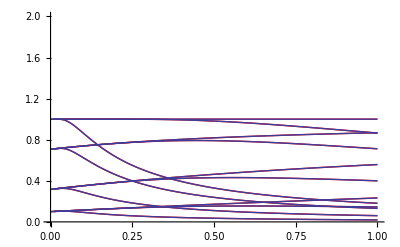

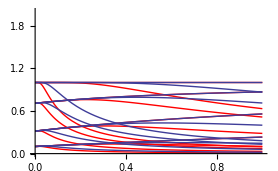
```mathematica
(*Wrong boundary condition*)
-Graphics-
```

```mathematica
Plot[(NDSolve@@#&/@Flatten[{{μ D[i[τ], τ]==i[τ, μ]-1+(1-ϵ)/(1+√ϵ)E^(-√(3 ϵ)τ), i[τ0]==i[τ0, -μ]}, {i},{τ, 0, τ0}}/.{{ϵ->0.01},{ϵ->0.1},{ ϵ->0.5}, {ϵ->1}}/.{{τ0->0.1},{τ0->1}, {τ0->10}},1]), {μ, 0, 1}]
```

```mathematica
(*Solving radiative transfer with Eddington approximation as a closure relation. And fixed photon destruction probability ϵ.*)
(*Module[{τ0, τmax},
τ0=1;
τmax=10^3;
Plot[
NDSolve[{μ i'[τ]==i[τ]-ϵ-(1-ϵ)j[τ],1/3 j''[τ]==ϵ(j[τ]-1) , i[τ0]==0,j[τmax]==1, 1/(√3) j'[0]==j[0]}, {j, i}, {τ, 0, τmax}(*,Method->{"Shooting", "StartingInitialConditions"->{j[0]==1.4}}*)]/.{{ϵ->1}},
{μ, 0, 1}, PlotRange->{Automatic,{0,2}}]
]*)
```

```mathematica
(*Module[{τ0, τmax, soln , soln1,soln2, A, B},*)
(*τ0=1;
τmax=10^4;
soln=NDSolve[#, x, {τ, 0, 10}]&/@({x''[τ]==3 ϵ x[τ], √3(x[0]+1)==x'[0], x[τmax]==0}/.{{ϵ->0.01},{ϵ->0.1},{ ϵ->0.5}, {ϵ->1}});
B=1/((√ϵ-1 )E^(-2 √(3ϵ)τmax)-(1+√ϵ));
A=B E^(-2 √(3ϵ)τmax);
soln1[t_]:=A E^(√(3ϵ)t)+B E^(-√(3ϵ)t)/.{{ϵ->0.01},{ϵ->0.1},{ ϵ->0.5}, {ϵ->1}};*)
(*soln2=DSolve[#, x,τ]&/@({x''[τ]==3 x[τ], √3(x[0]+1)==x'[0], x[τmax]==0}/.{{ϵ->0.01},{ϵ->0.1},{ ϵ->0.5}, {ϵ->1}});*)
(*{
LogPlot[Abs[x[t]]/.soln, {t, 0, 10}],
LogPlot[100Abs[((x[t]/.soln)-(soln1[t]))/(soln1[t])], {t, 0, 10}]}*)
```

```mathematica
(*τmax=40;
ϵ=0.5;
τ0=1;
jsoln=NDSolve[{j'[τ]==u[τ] (j[τ]-1), u'[τ]==3*ϵ-u[τ]/(j[τ]-1), u[0]==√3, j[τmax]==1}, {u, j}, {τ, 0, τmax}, Method->{"Shooting", "StartingInitialConditions"->{j[0] == 0.5,u[0] == √3}}];
ourj=j[τ]/.jsoln;
soln=Table[{μ/10.,(μ/10. i[0]/.NDSolve[{μ/10  i'[τ]==i[τ]-ϵ-(1-ϵ)(ourj), i[τ0]==0}, i, {τ, 0, τ0}])//First}, {μ, 1, 10, 1}];
soln//ListLinePlot*)
```

```mathematica
(*ϵ={0.01, 0.1, 0.5, 1}
τ0=ArcTan/@{10, 1, 0.1};
jsoln=j[τ]/.Table[(NDSolve[{(Cos[τ])^2 D[u[τ](j[τ]-1)(Cos[τ])^2, τ]==3ϵ[[k]] (j[τ]-1), j'[τ]==(j[τ]-1)u[τ], u[0] == √3,j[1.56]==1}, {u, j}, {τ, 0, 1.56}, Method->{"Shooting", "StartingInitialConditions"->{j[0] == 0.5,u[0] == √3}}]), {k ,1, ϵ//Length}]
soln=Table[{μ/10, If[μ==0,(ϵ[[k]]+(1-ϵ[[k]])  ((jsoln[[k]])//First /.τ->0 )   ),(i[0]/.NDSolve[{ μ/10. (Cos[τ])^2 i'[τ]==i[τ]-ϵ[[k]]-(1-ϵ[[k]])((jsoln[[k]])//First), i[τ0[[l]]]==0},{i}, {τ,0 ,τ0}])//First]}, {l, 1,τ0//Length}, {k, 1, ϵ//Length},  {μ, 0, 10,1} ]*)
```

```mathematica
(*ϵ={0.01,0.1,0.5,  1}
τ0=ArcTan/@{10, 1, 0.1};
jsoln=j[τ]/.Table[(NDSolve[{(Cos[τ])^2 D[j[τ] u[τ](Cos[τ])^2, τ]==3ϵ[[k]] (j[τ]-1),j'[τ]==j[τ] u[τ],  u[0]==√3,j[1.56]==1}, {j, u}, {τ, 0, 1.56}(*     , Method->{"Shooting", "StartingInitialConditions"->{j[π/2] ==1,j'[0] == √3}}*)]), {k ,1, ϵ//Length}];
(*soln=Table[{μ/10, If[μ==0,(ϵ[[k]]+(1-ϵ[[k]])  (     (jsoln[[k]]) /.τ->0 ) //First  ),(i[0]/.NDSolve[{ μ/10. (Cos[τ])^2 i'[τ]==i[τ]-ϵ[[k]]-(1-ϵ[[k]])((jsoln[[k]])//First), i[τ0[[l]]]==0},{i}, {τ,0 ,τ0}])//First]}, {l, 1,τ0//Length}, {k, 1, ϵ//Length},  {μ, 0, 10,1} ];*)

ListLinePlot/@soln//Show*)
```

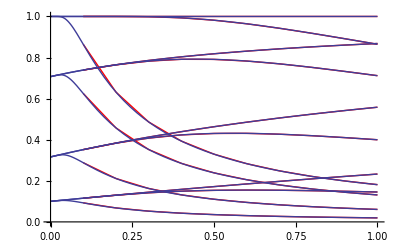

```mathematica
Module[{ϵ, τ0, τmax, jsoln, soln, p},
ϵ={0.01, 0.1, 0.5, 1};
τmax=10^4;
τ0={10, 1, 0.1};
jsoln=j[τ]/.Table[(NDSolve[{j''[τ]==3 ϵ[[k]] (j[τ]-1),j[0]==(1-1/(1+√ϵ[[k]])),j'[0]==√3(1-1/(1+√ϵ[[k]]))}, {j, j'}, {τ,0 ,τ0//Max}]), {k ,1, ϵ//Length}];

soln=Table[{μ/10,(i[0]/.NDSolve[{ μ/10 i'[τ]==i[τ]-ϵ[[k]]-(1-ϵ[[k]])(jsoln[[k]]//First), i[ τ0[[l]]  ]==bdry[ μ/10, ϵ[[k]],τ0[[l]]   ]},{i}, {τ,0 ,τ0[[l]  ]}])//First}, {l, 1,τ0//Length}, {k, 1,ϵ//Length},  {μ, 1, 10,1} ];
p= ListLinePlot[#, PlotStyle->Directive[Red]]&/@soln;
Show[p, fig3 ]]
```

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. The computed solution may match the boundary conditions poorly.

NDSolve::berr: There are significant errors {0.`, -1.7095813653611458`*^-10, 3.6135477894106575`*^26} in the boundary value residuals. Returning the best solution found.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. The computed solution may match the boundary conditions poorly.

NDSolve::berr: There are significant errors {0.`, 4.1145065132752734`*^-10, 331031.00908485684`} in the boundary value residuals. Returning the best solution found.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. The computed solution may match the boundary conditions poorly.

General::stop: Further output of NDSolve will be suppressed during this calculation.

NDSolve::berr: There are significant errors {0.`, -3.017620597844939`*^-10, -0.015349652300715166`} in the boundary value residuals. Returning the best solution found.

General::stop: Further output of NDSolve will be suppressed during this calculation.

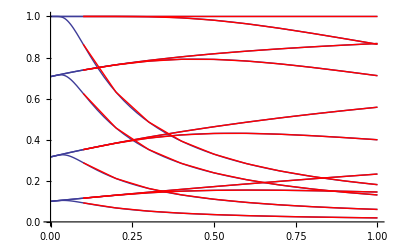

```mathematica
Module[{ϵ, τ0, τmax, soln},
ϵ={0.01, 0.1, 0.5, 1};
τmax=90;
τ0={10, 1, 0.1};
soln=Table[{μ/10, If[μ==0,(ϵ[[k]]+(1-ϵ[[k]])j[0]/.NDSolve[{j''[τ]==3 ϵ[[k]] (j[τ]-1),√3 j[0]==j'[0], j[τmax]==1}, j, {τ,0 ,12}])//First,(i[0]/.NDSolve[{j''[τ]==3 ϵ[[k]] (j[τ]-1), √3 j[0]==j'[0], j[τmax]==1, μ/10. i'[τ]==i[τ]-ϵ[[k]]-(1-ϵ[[k]])j[τ], i[τ0[[l]]]==bdry[μ/10, ϵ[[k]], τ0[[l]]]},{i, j}, {τ,0 ,12}])//First]}, {l, 1,τ0//Length}, {k, 1, ϵ//Length},  {μ, 1, 10,1} ];
Show[fig3, ListLinePlot[#, PlotStyle->Directive[Red]]&/@soln]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: There are significant errors {-0.0002993155882521359`, -1.41518944059524`} in the boundary value residuals. Returning the best solution found.

NDSolve::nderr: Error test failure at τ == 52.1031; unable to continue.

NDSolve::nderr: Error test failure at τ == 52.5374; unable to continue.

NDSolve::nderr: Error test failure at τ == 46.8875; unable to continue.

General::stop: Further output of NDSolve will be suppressed during this calculation.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

NDSolve::berr: There are significant errors {1.66472433884912`*^9, -6.732392421326949`*^-12} in the boundary value residuals. Returning the best solution found.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

NDSolve::berr: There are significant errors {-0.999999999999998`, 0.`} in the boundary value residuals. Returning the best solution found.

General::stop: Further output of NDSolve will be suppressed during this calculation.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

General::stop: Further output of FindRoot will be suppressed during this calculation.

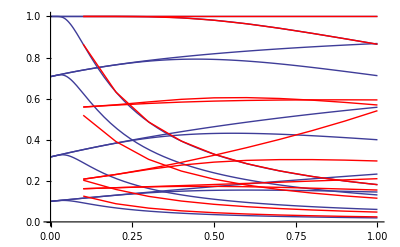

```mathematica
Module[{ϵ, τ0, τmax, soln, jsoln},
ϵ={0.01, 0.1, 0.5, 1};
τmax=90;
τ0={10, 1, 0.1};
jsoln=j[τ]/.Table[NDSolve[{u'[τ]==-j[τ](u[τ])^2+3ϵ [[k]](j[τ]-1), j'[τ]==j[τ] u[τ], j[τmax]==1, u[0]==√3}, {j, u}, {τ, 0, τmax}, Method->{"Shooting", "StartingInitialConditions"->{j[0]==0.1, u[0]==√3}}], {k, 1, ϵ//Length}];
soln=Table[{μ/10,(i[0]/.NDSolve[{ μ/10 i'[τ]==i[τ]-ϵ[[k]]-(1-ϵ[[k]])(jsoln[[k]]//First), i[ τ0[[l]]  ]==bdry[ μ/10, ϵ[[k]],τ0[[l]]   ]},{i}, {τ,0 ,τ0[[l]  ]}])//First}, {l, 1,τ0//Length}, {k, 1,ϵ//Length},  {μ, 1, 10,1} ];
Show[fig3, ListLinePlot[#, PlotStyle->Directive[Red]]&/@soln]]
```

```mathematica
(*Analytic intensity Equation 33 from Fukue paper*)
```